```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["/Users/zackarywindham/Research/Post-Minkowski/PMdata.csv"]
{x1,y1,z1,px1,py1,pz1,x2,y2,z2,px2,py2,pz2,x3,y3,z3,px3,py3,pz3,hamil}=data;
```

/Users/zackarywindham/Research/Post-Minkowski

{{-8.58684,-3.90139,0.795333,4.50902,0.554011,-7.55523,-16.6143,1187,-11678.4,-11688.2,-11698.1,-11707.9,-11717.7,-11727.5,-11737.3},17,{1}}
 |  |  |  |

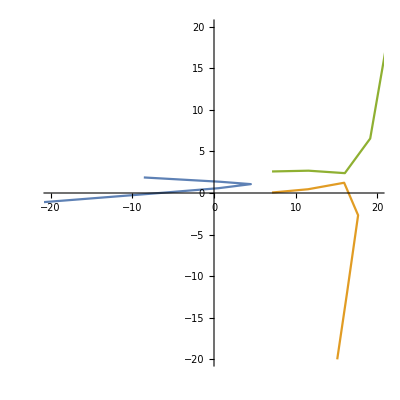

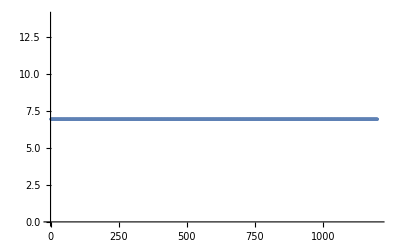

```mathematica
ListPlot[{Transpose[{data[[1]],data[[2]]}],Transpose[{data[[7]],data[[8]]}],Transpose[{data[[13]],data[[14]]}]},AspectRatio->1,PlotRange->{{-20,20},{-20,20}},Joined->True]
ListPlot[Delete[hamil,1]]
```